## Refraction directly

{{ne→0.972898},{ne→3.88964}}

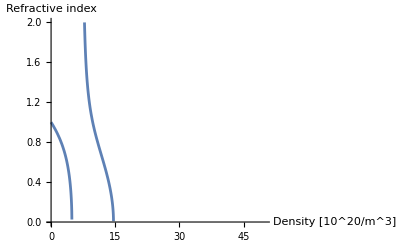

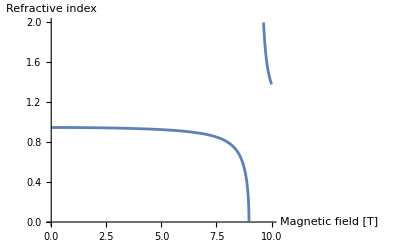

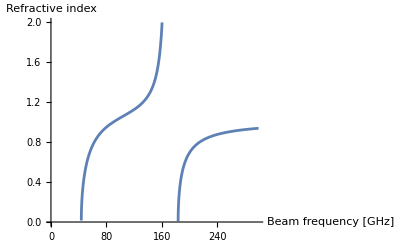

43.8564

166.286

183.819

```mathematica
Clear["`*"]
e=1.602176634*10^(-19);
ϵ0=8.854187818*10^(-12);
me=9.1093837139*10^(-31);
mp=1.66053906892*10^(-27);

plasmaFreq=Sqrt[ne*10^20*e^2/(ϵ0*me)];
cyclotronFreq=(e*B/me);
ionCyclotronFreq=((Z*e)*B/(A*mp));

upperHybridFreq=Sqrt[plasmaFreq^2+cyclotronFreq^2];

w=f*2π*10^9;
wl=0.5(Sqrt[cyclotronFreq^2+4*plasmaFreq^2]-cyclotronFreq);
wr=0.5(Sqrt[cyclotronFreq^2+4*plasmaFreq^2]+cyclotronFreq);
nX=Sqrt[(w^2-wl^2)*(w^2-wr^2)]/Sqrt[(w^2-upperHybridFreq^2)*w^2];(*mm wave equation 2.98*)

nX1=Sqrt[1-((plasmaFreq/w)^2)*(w-plasmaFreq^2)/(w-cyclotronFreq^2-plasmaFreq^2)];(*mm-wave equation 4.52*)

nX0 = Sqrt[(((w+ionCyclotronFreq)*(w-cyclotronFreq)-plasmaFreq^2)((w-ionCyclotronFreq)*(w+cyclotronFreq)-plasmaFreq^2))/((w^2-cyclotronFreq^2)(w^2-ionCyclotronFreq^2)+plasmaFreq^2*(cyclotronFreq*ionCyclotronFreq-w^2))];(*From lecture slide*)

nO = Sqrt[1-(plasmaFreq^2)/(w^2)];(*mm-wave equation 2.97*)

Solve[nX==0,ne];
Solve[nX==0,ne]/.{A->2,Z->1.5,B->3,f->140}
Solve[nO==0,ne];

(cyclotronFreq/.{B->5})/(2π*10^9);

Plot[nX/.{f->280,B->5},{ne,0,100},PlotRange->{{0,50},{0,2}}, AxesLabel->{"Density [10^20/m^3]", "Refractive index"}]
(*Plot[nX0/.{f->280,B->5,Z-> 1.5,A->2},{ne,0,10},PlotRange->{{0,10},{0,2}}, AxesLabel->{"Density [10^20/m^3]", "Refractive index"}]*)
Plot[nX/.{f->280,ne->1},{B,0,10},PlotRange->{{0,10},{0,2}}, AxesLabel->{"Magnetic field [T]", "Refractive index"}]
Plot[nX/.{B->5,ne->1},{f,0,300},PlotRange->{{0,300},{0,2}}, AxesLabel->{"Beam frequency [GHz]", "Refractive index"}]
(wl/(2π*10^9))/.{B->5,ne->1}
(upperHybridFreq/(2π*10^9))/.{B->5,ne->1}
(wr/(2π*10^9))/.{B->5,ne->1}
```

## 1D region plots

```mathematica
ner=ne/.(Solve[wr/(2π*10^9)==f,ne])[[1]];(*/.{B->3,f->140}*)
neuh=ne/.(Solve[upperHybridFreq/(2π*10^9)==f,ne])[[1]];
nel=ne/.(Solve[wl/(2π*10^9)==f,ne])[[1]];

(*RegionPlot[{ner<ne<neuh, nel<ne},{ne,0,5},{p,0,1},PlotLegends->{"R-cuttoff","X-mode transmission"},FrameLabel->{"Density [10^20/m^3]", " "}]*)
Manipulate[Show[RegionPlot[{ne<ner/.{B->BPlasma,f->fin},( neuh/.{B->BPlasma,f->fin})<ne<(nel/.{B->BPlasma,f->fin})},{ne,0,5},{p,0,2},PlotLegends->{"Fast-X-mode transmission","Slow-X-mode transmission"},FrameLabel->{"Density [10^20/m^3]", "Index of refraction"}],Plot[nX/.{B->BPlasma,f->fin},{ne,0,5},PlotStyle->Red,PlotRange->{{0,5},{0,2}}],AspectRatio->1/2.5],{{fin,140},50,300,Appearance->"Labeled" }, {{BPlasma,3},0,8,Appearance->"Labeled" }]

Buh=B/.(Solve[upperHybridFreq/(2π*10^9)==f,B])[[2]];
Br=B/.(Solve[nX==0,B])[[2]];

(*RegionPlot[{ner<ne<neuh, nel<ne},{ne,0,5},{p,0,1},PlotLegends->{"R-cuttoff","X-mode transmission"},FrameLabel->{"Density [10^20/m^3]", " "}]*)
Manipulate[Show[RegionPlot[{B<Br/.{ne->nePlasma,f->fin},( Buh/.{ne->nePlasma,f->fin})<B},{B,0,5},{p,0,2},PlotLegends->{"Fast-X-mode transmission","Slow-X-mode transmission"},FrameLabel->{"Magnetic field [T]", "Index of refraction"}],Plot[nX/.{ne->nePlasma,f->fin},{B,0,50},PlotStyle->Red,PlotRange->{{0,5},{0,2}}],AspectRatio->1/2.5],{{fin,140},50,300,Appearance->"Labeled" }, {{nePlasma,1},0,5,Appearance->"Labeled" }]

(*RegionPlot[{ner<ne<neuh, nel<ne},{ne,0,5},{p,0,1},PlotLegends->{"R-cuttoff","X-mode transmission"},FrameLabel->{"Density [10^20/m^3]", " "}]*)
Manipulate[Show[RegionPlot[{((wr/(2π*10^9))/.{B->BPlasma,ne->nePlasma})<f,((upperHybridFreq/(2π*10^9))/.{B->BPlasma,ne->nePlasma})>f>((wl/(2π*10^9))/.{B->BPlasma,ne->nePlasma})},{f,0,300},{p,0,2},PlotLegends->{"Fast-X-mode transmission","Slow-X-mode transmission"},FrameLabel->{"Frequency [Ghz]", "Index of refraction"}],Plot[nX/.{B->BPlasma,ne->nePlasma},{f,0,300},PlotStyle->Red,PlotRange->{{0,300},{0,2}}],AspectRatio->1/2.5],{{nePlasma,1},0,5,Appearance->"Labeled" }, {{BPlasma,3},0,8,Appearance->"Labeled" }]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.